# CNN Project

## Review

Baoxiang Pan
2017.7.13

## Data

Precipitation

```mathematica
SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
year=1948;
precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
mlat=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lat"}][[48;;]];
mlon=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lon"}][[21;;65]];
precip=precip /. x_/; x< 0 ->nan;
precip[[;;,32;;,26;;]]=nan;
Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	   t,tt},
	t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
	tt=Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t];
	Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt]];
```

```mathematica
precip=Block[{mlat,mlon,tt},
	SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
	mlat=Import["precip.V1.0.1948.nc",{"Datasets","lat"}][[48;;]];
	mlon=Import["precip.V1.0.1948.nc",{"Datasets","lon"}][[21;;65]];
	tt=Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	       t},
			t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
			Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t]];
	Table[Block[{precip},
		precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
		precip=precip /. x_/; x< 0 ->nan;
		precip[[;;,32;;,26;;]]=nan;
		Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt];
		precip],{year,1948,2006}]];
```

```mathematica
Dimensions[precip]
```

{732,73,45}

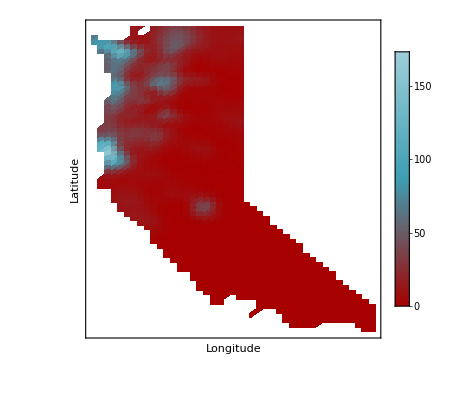

```mathematica
ListDensityPlot[precip[[1,;;,;;]],
	PlotLegends->Automatic,
	BaseStyle->20,
	Frame->True,
	PlotRange->Full,
	FrameLabel->{"Longitude","Latitude"},
	FrameTicks->None,
	PlotRange->Full]
```

Sea Level Pressure

```mathematica
SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/SLP"];
year=1948;
slp=Import["slp."<>ToString[year]<>".nc",{"Datasets","slp"}][[;;,13;;28,89;;99]];
mlat=Import["slp."<>ToString[year]<>".nc",{"Datasets","lat"}][[13;;28]];
mlon=Import["slp."<>ToString[year]<>".nc",{"Datasets","lon"}][[89;;99]];
```

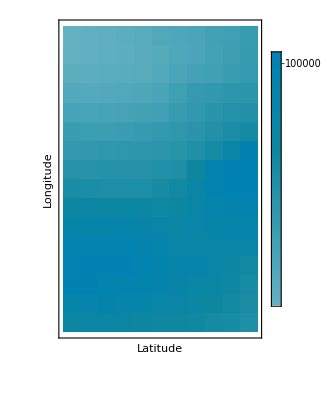

```mathematica
MatrixPlot[Mean[slp[[1;;4,;;,;;]]],
	PlotLegends->Automatic,
	BaseStyle->20,
	Frame->True,
	PlotRange->Full,
	FrameLabel->{"Longitude","Latitude"},
	FrameTicks->None,
	PlotRange->Full]
```

## Network Structure

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

Item duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

Subitem nam liber tempor cum soluta nobis eleifend option congue nihil imperdiet doming id quod mazim placerat facer possim assum.

Subitem typi non habent claritatem insitam; est usus legentis in is qui facit eorum claritatem.

### Second level section heading

Text duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.